# Chaotic-string computations

## Main function definitions

The following are the CellularAutomaton function definitions for the various chaotic strings:

```mathematica
t[2,x_]:=ChebyshevT[2,x];t[3,x_]:=ChebyshevT[3,x];
k[n_,x_,b_]:=b*t[n,x]+(1-b)*x;
f[{n_,b_,s_},a_,{x_,y_,z_}]:=(t[n,y]+a*Mean[{s*k[n,x,b]-t[n,y],s*k[n,z,b]-t[n,y]}]);

f2Ap[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{2,1,+1},a,{x,y,z}]},v,p]; (* 2 A^+ *)
f2Am[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{2,1,-1},a,{x,y,z}]},v,p]; (* 2 A^- *)
f2Bp[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{2,0,+1},a,{x,y,z}]},v,p]; (* 2 B^+ *)
f2Bm[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{2,0,-1},a,{x,y,z}]},v,p]; (* 2 B^- *)
f3Ap[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{3,1,+1},a,{x,y,z}]},v,p]; (* 3 A^+ *)
f3Am[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{3,1,-1},a,{x,y,z}]},v,p]; (* 3 A^- *)
f3Bp[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{3,0,+1},a,{x,y,z}]},v,p]; (* 3 B^+ *)
f3Bm[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>f[{3,0,-1},a,{x,y,z}]},v,p]; (* 3 B^- *)
```

For efficiency, we can use the following equivalent forms of the above functions:

```mathematica
t[2,x_]:=t[2,x]=-1+2 x^2;
t[3,x_]:=t[3,x]=-3 x+4 x^3;

f2Ap[a_,v_,p_]:=f2Ap[a,v,p]=CellularAutomaton[{{x_,y_,z_}:>-1+2 y^2+1/2 a (2 x^2-4 y^2+2 z^2)},v,p];
f2Am[a_,v_,p_]:=f2Am[a,v,p]=CellularAutomaton[{{x_,y_,z_}:>-1+2 y^2+1/2 a (4-2 x^2-4 y^2-2 z^2)},v,p];
f2Bp[a_,v_,p_]:=f2Bp[a,v,p]=CellularAutomaton[{{x_,y_,z_}:>-1+2 y^2+1/2 a (2+x-4 y^2+z)},v,p];
f2Bm[a_,v_,p_]:=f2Bm[a,v,p]=CellularAutomaton[{{x_,y_,z_}:>-1+2 y^2+1/2 a (2-x-4 y^2-z)},v,p];
f3Ap[a_,v_,p_]:=f3Ap[a,v,p]=CellularAutomaton[{{x_,y_,z_}:>-3 y+4 y^3+1/2 a (-3 x+4 x^3+6 y-8 y^3-3 z+4 z^3)},v,p];
f3Am[a_,v_,p_]:=f3Am[a,v,p]=CellularAutomaton[{{x_,y_,z_}:>-3 y+4 y^3+1/2 a (3 x-4 x^3+6 y-8 y^3+3 z-4 z^3)},v,p];
f3Bp[a_,v_,p_]:=f3Bp[a,v,p]=CellularAutomaton[{{x_,y_,z_}:>-3 y+4 y^3+1/2 a (x+6 y-8 y^3+z)},v,p];
f3Bm[a_,v_,p_]:=f3Bm[a,v,p]=CellularAutomaton[{{x_,y_,z_}:>-3 y+4 y^3+1/2 a (-x+6 y-8 y^3-z)},v,p];
```

## For the entire range of the coupling parameter a ∈ [0, 1]

### Lattice size = 1000

{2025,10,15,20,23,57.776881}

{2025,10,15,20,40,51.364737}

16.8931309 minutes

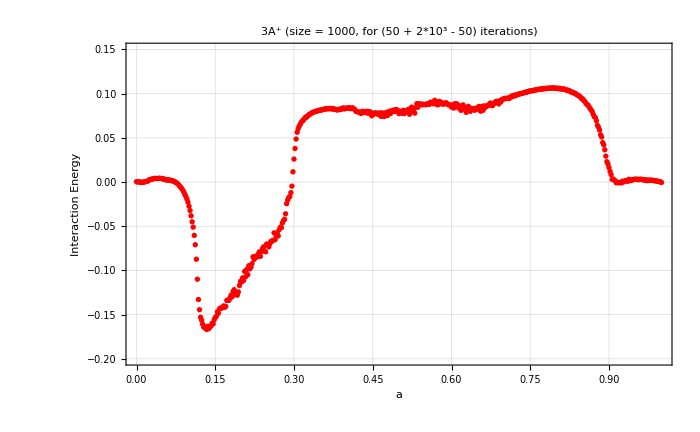

```mathematica
a=N[#,{∞,10^4}]&/@Range[0,1,2*10^-3]; (* range of values for the coupling parameter a *)

d=1*10^-2; (* magnitude of the range for random initial values *)
u=1*10^3; (* size of the lattice *)
v:=RandomReal[{-d,d},u]; (* lattice values *)
q=50; (* "transient time" *)
p=q+2*10^3; (* total number of iterations *)

SeedRandom[1,Method->"Rule30CA"];

f3ApData[a_]:=f3ApData[a]=Mean[MapThread[Dot,{#,RotateRight/@#}&[Drop[f3Ap[a,v,p],1+q]]]]/(2*u); (* computation of the interaction energy for the chaotic string 3 A^+ *)

t1=Date[]
f3ApDataA=Thread[{#,ParallelMap[f3ApData,#]}]&[a];
t2=Date[]

Print[((t2[[-3]]-t1[[-3]])*60*60+(t2[[-2]]-t1[[-2]])*60+(t2[[-1]]-t1[[-1]]))/60," minutes"];

ListPlot[f3ApDataA,Frame->True,PlotLabel->"3A^+",FrameLabel->{"a","Interaction Energy"},GridLines->Automatic,PlotRange->{Automatic,{-0.20,0.15}},PlotStyle->Red]
```

## For the low-coupling range a ∈ [0, 0.018]

### Lattice size = 1000

{2025,10,16,12,50,18.014926}

{2025,10,16,14,51,43.911993}

121.4316178 minutes

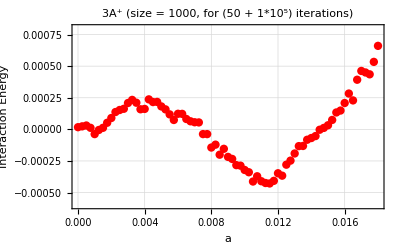

```mathematica
a=N[#,{∞,10^4}]&/@Range[0,18*10^-3,250*10^-6];

d=1*10^-2;
u=1*10^3;
v:=RandomReal[{-d,d},u];
q=50;
p=q+1*10^5;

SeedRandom[1,Method->"Rule30CA"];

f3ApData[a_]:=f3ApData[a]=Mean[MapThread[Dot,{#,RotateRight/@#}&[Drop[f3Ap[a,v,p],1+q]]]]/(2*u);

t1=Date[]
f3ApDataA=Thread[{#,ParallelMap[f3ApData,#]}]&[a];
t2=Date[]

Print[((t2[[-3]]-t1[[-3]])*60*60+(t2[[-2]]-t1[[-2]])*60+(t2[[-1]]-t1[[-1]]))/60," minutes"];

ListPlot[f3ApDataA,Frame->True,PlotLabel->"3A^+",FrameLabel->{"a","Interaction Energy"},GridLines->Automatic,PlotRange->{Automatic,{-0.0006,0.0008}},PlotStyle->Red]
```

### Lattice size = 4

```mathematica
Exit[]
```

{2025,10,18,7,46,37.120041}

{2025,10,18,17,8,43.023805}

562.0983961 minutes

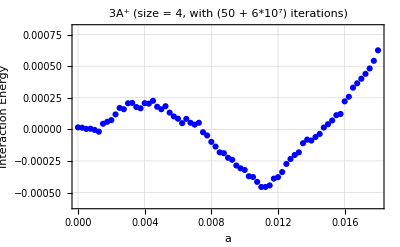

```mathematica
t[2,x_]:=-1+2 x^2;
t[3,x_]:=-3 x+4 x^3;
f2Ap[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>-1+2 y^2+1/2 a (2 x^2-4 y^2+2 z^2)},v,p];
f2Am[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>-1+2 y^2+1/2 a (4-2 x^2-4 y^2-2 z^2)},v,p];
f2Bp[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>-1+2 y^2+1/2 a (2+x-4 y^2+z)},v,p];
f2Bm[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>-1+2 y^2+1/2 a (2-x-4 y^2-z)},v,p];
f3Ap[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>-3 y+4 y^3+1/2 a (-3 x+4 x^3+6 y-8 y^3-3 z+4 z^3)},v,p];
f3Am[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>-3 y+4 y^3+1/2 a (3 x-4 x^3+6 y-8 y^3+3 z-4 z^3)},v,p];
f3Bp[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>-3 y+4 y^3+1/2 a (x+6 y-8 y^3+z)},v,p];
f3Bm[a_,v_,p_]:=CellularAutomaton[{{x_,y_,z_}:>-3 y+4 y^3+1/2 a (-x+6 y-8 y^3-z)},v,p];
a=N[#,{∞,10^4}]&/@Range[0,18*10^-3,250*10^-6];

d=1*10^-2;
u=4;
v:=RandomReal[{-d,d},u];
q=50;
p=q+6*10^7;

SeedRandom[1,Method->"Rule30CA"];

f3ApData[a_]:=Mean[MapThread[Dot,{#,RotateRight/@#}&[Drop[f3Ap[a,v,p],1+q]]]]/(2*u);

t1=Date[]
f3ApDataA=Thread[{#,ParallelMap[f3ApData,#]}]&[a];
t2=Date[]

Print[((t2[[-3]]-t1[[-3]])*60*60+(t2[[-2]]-t1[[-2]])*60+(t2[[-1]]-t1[[-1]]))/60," minutes"];

ListPlot[f3ApDataA,Frame->True,PlotLabel->"3A^+",FrameLabel->{"a","Interaction Energy"},GridLines->Automatic,PlotRange->{Automatic,{-0.0006,0.0008}},PlotStyle->Red]
```

### Both results combined